# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Assignment 06

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1.

We are given a single-step geometric binomial pricing lattice as the model for the price dynamics of a stock with current price S(0):

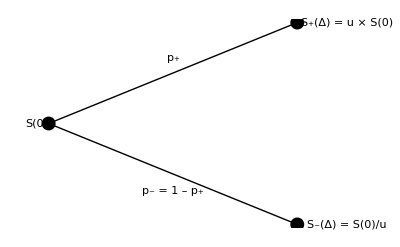

Consider a case in which S(0)  = 95, Δ = 0.25, u = 1.1, and the risk free rate of return r = 1.5%, then...

Show that the market for S(t) is arbitrage free.

What is the risk neutral measure?

What is the price at t=0 for an at-the-money put?

## Question 2.

For an underlying whose price dynamic follows the following SDE

ⅆS(t)=μ S(t)ⅆt+σ S(t) ⅆW(t)

Let

X(t)=(S(t))^-1

Use Itô's lemma to determine the SDE which describes the price dynamics of X(t), assuming S(0)>0.

## Question 3.

Consider a European capped-call option. With S(t) the price of the underlying and F(t) the price of the option, the capped-call gives the holder the right to exercise the option at expiry with value of a put with strike K whose value, however, is capped at a maximum pay-out C where K<C. Thus, the value at expiry T can be expressed by

F(T)=min[ max[ S(T)-K, 0 ], C ]

Assume the risk free rate is r with continuous compounding. Express the value of the option at time t<T in terms of vanilla European options with appropriately chosen parameters and, if necessary, any cash position.

## Question 4.

Consider a security priced S(t) with σ=0.22 where the risk free rate r=0.01.

Use FinancialDerivative[ ] to plot the values of a European call option for a strike K=102 and expiry T=0.5 at t=0.25 for 60≤S(t)≤140.

With the same parameters above, use FinancialDerivative[ ] to plot the values of an at-the-money European call option at t=0.25 for values of 0.1≤σ≤0.3.